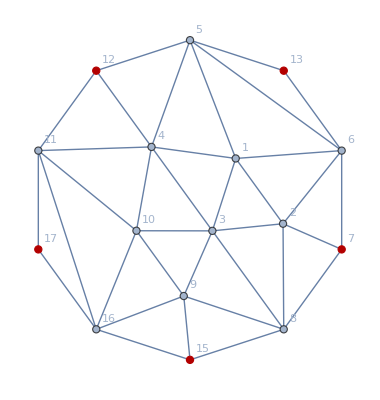

```mathematica
Graph[pl8[0], GraphHighlight->{12,13,7,15,17,12<->13,12<->7,7<->13}, GraphLayout->"TutteEmbedding",VertexLabels->"Name"]
```

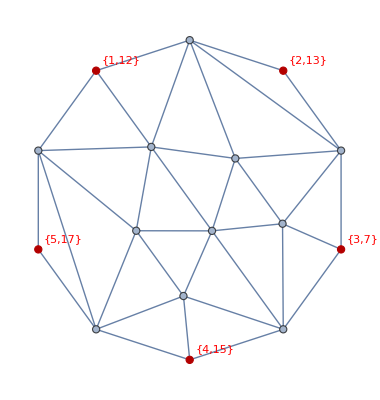

```mathematica
g0=Graph[pl8[0], GraphHighlight->{12,13,7,15,17,12<->13,12<->7,7<->13}, GraphLayout->"TutteEmbedding",VertexLabels->{12->Style[{Style[1,Bold,Underlined],12},Red],13->Style[{Style[2,Bold,Underlined],13},Red],7->Style[{Style[3,Bold,Underlined],7},Red],15->Style[{Style[4,Bold,Underlined],15},Red],17->Style[{Style[5,Bold,Underlined],17},Red]}]
```

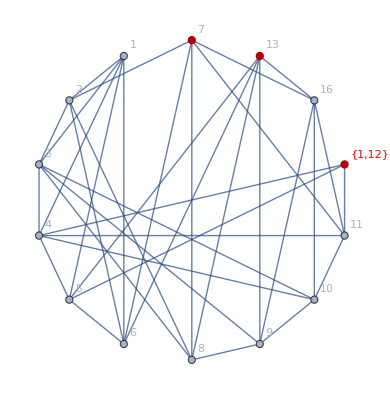

```mathematica
g24=Graph[VertexContract[VertexContract[g0,{13,15}],{7,17}],GraphLayout->"CircularEmbedding",GraphHighlight->{12,13,7,15,17,12<->13,12<->7,7<->13}, VertexLabels->"Name"]
```

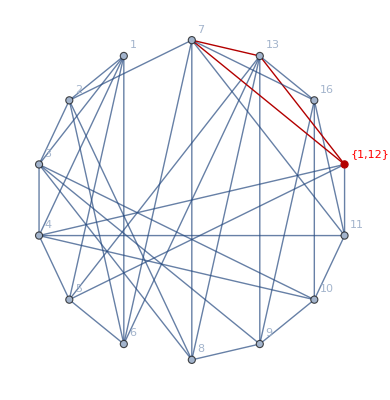

```mathematica
g2435=Graph[EdgeAdd[VertexContract[VertexContract[g0,{13,15}],{7,17}],{13<->12,12<->7,7<->13}],GraphLayout->"CircularEmbedding", VertexLabels->"Name"]
```

```mathematica
ChromaticPolynomial[g2435,4]
```

0

```mathematica
ChromaticPolynomial[g2435,5]/120
```

1586

```mathematica
TableForm[Sort[Table[e<->ChromaticPolynomial[EdgeDelete[g2435,e],4]/24,{e,EdgeList[g2435]}],#1[[2]]<#2[[2]]&]]
```

11<->12<->2
11<->16<->2
9<->16<->2
8<->9<->2
5<->6<->2
5<->12<->2
2<->8<->2
2<->6<->2
3<->4<->3
7<->16<->4
7<->6<->4
13<->16<->4
13<->6<->4
12<->7<->5
12<->13<->5
7<->8<->5
13<->8<->5
10<->11<->6
10<->16<->6
9<->10<->6
4<->5<->6
4<->11<->6
4<->10<->6
3<->10<->6
3<->9<->6
2<->3<->6
1<->6<->6
1<->5<->6
1<->4<->6
1<->3<->6
1<->2<->6
4<->12<->7
3<->8<->7
7<->11<->8
7<->2<->8
13<->9<->8
13<->5<->8
7<->13<->11

```mathematica
edges234=Map[UndirectedEdge[#[[1]],#[[2]]]&,Sort[Map[{Min[#[[1]],#[[2]]],Max[#[[1]],#[[2]]]}&,Select[EdgeList[g2435],ChromaticPolynomial[EdgeDelete[g2435,#],4]/24==2&]]]]
```

{2<->6,2<->8,5<->6,5<->12,8<->9,9<->16,11<->12,11<->16}

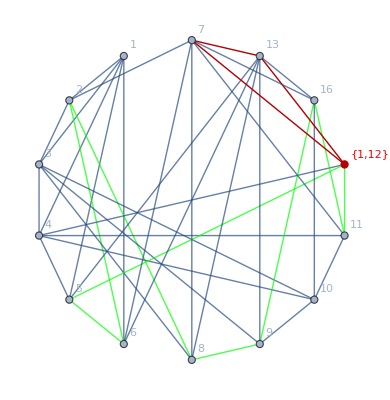

```mathematica
Graph[g2435,EdgeStyle->Map[#->Directive[Thick,Green]&,edges234]]
```

```mathematica
Sort[DeleteDuplicates[Flatten[Map[{#[[1]],#[[2]]}&,edges234]]]]
```

{2,5,6,8,9,11,12,16}

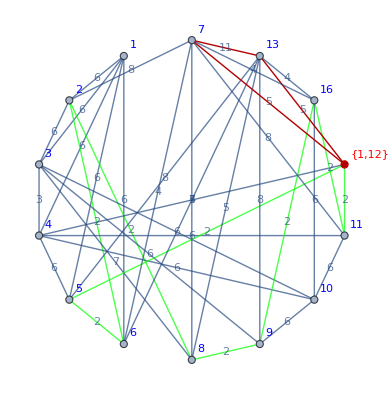

```mathematica
Graph[g2435,EdgeStyle->Map[#->Directive[Thick,Green]&,Select[EdgeList[g2435],ChromaticPolynomial[EdgeDelete[g2435,#],4]/24==2&]],EdgeLabels->Table[e->(ChromaticPolynomial[EdgeContract[g2435,e],4]/24),{e,EdgeList[g2435]}],VertexLabelStyle->Blue]
```

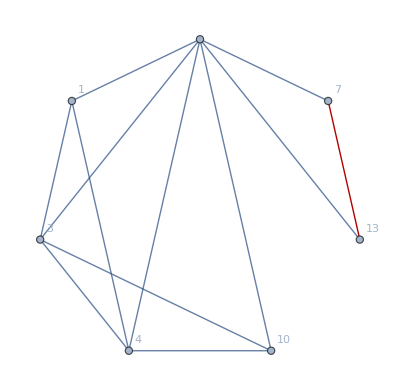

```mathematica
EdgeContract[g2435,Select[EdgeList[g2435],ChromaticPolynomial[EdgeDelete[g2435,#],4]/24==2&]]
```

```mathematica
Table[ChromaticPolynomial[VertexDelete[g2435,v],4]/24,{v,VertexList[g2435]}]
```

{10,8,16,16,8,6,7,8,10,8,7,6,26,26}

```mathematica
FindContraction[g_]:=Block[{edges,e,i, sub,h, result=False,keep,chroms,first},
counted++;
vertexCount=VertexCount[g];
If[vertexCount< 5, 
result=False,
If[(FindClique[g,{5}]≠{}),
result=True
,
edges=EdgeList[g];
chroms=Association[];
For[i=1,i≤Length[edges],i++,
work="calcaulating chroms "<>ToString[i];
e=edges[[i]];
h=EdgeContract[g,e];
chroms[e]=ChromaticPolynomial[h,4];
];
work="Sorting edges";
edges=Sort[edges,chroms[#1]<chroms[#2]&];
first=chroms[First[edges]];
edges=Select[edges,chroms[#]≤(2*first)&];
work="Traversing edges";
For[i=1,i≤Length[edges],i++,
e=edges[[i]];
work="Traversing edges "<>ToString[e];
h=EdgeContract[g,e];
keep=currentEdges;
currentEdges=Append[currentEdges,e];
sub=FindContraction[h];
currentEdges=keep;
If[sub, 
solution2=Prepend[solution2,e];
solution=Prepend[solution,{e,Graph[EdgeList[g],GraphHighlight->e,VertexLabels->"Name",GraphLayout->"CircularEmbedding", GraphHighlightStyle->"Thick"]}];
Print[e]; result=sub;i=Length[edges]+1
];
]
]
];
result
]
```

7<->4

11<->7

1<->10

5<->1

5<->16

6<->5

6<->9

13<->6

11<->12

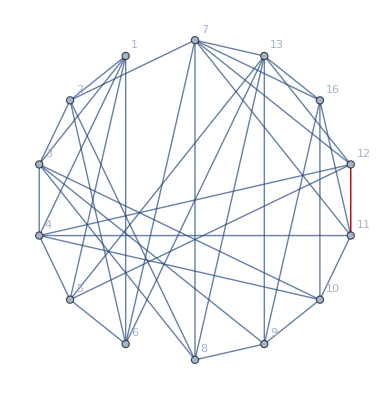
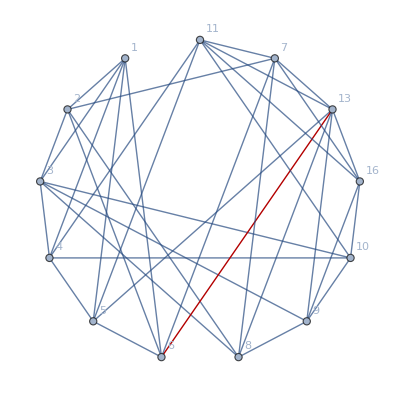
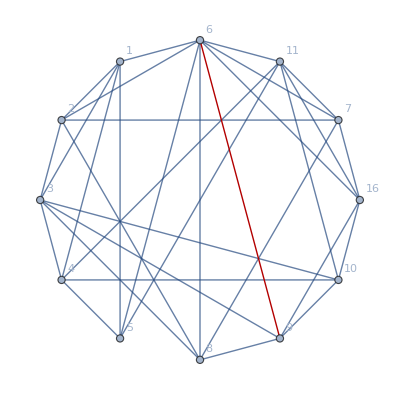
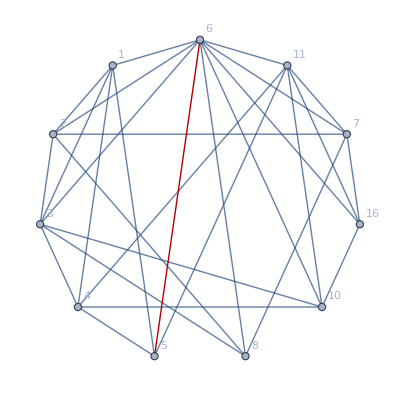
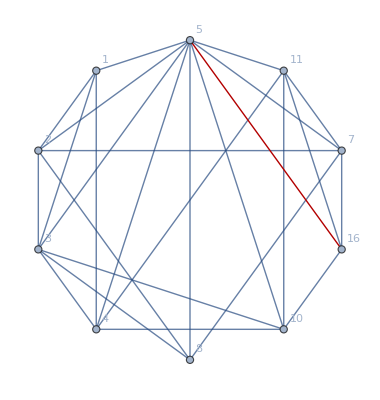
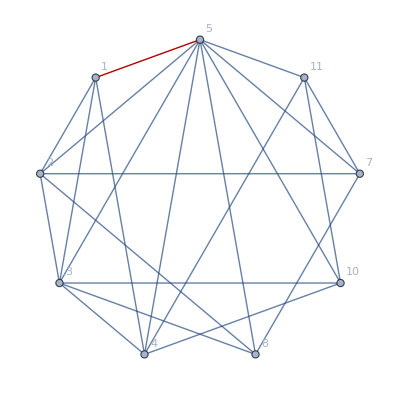
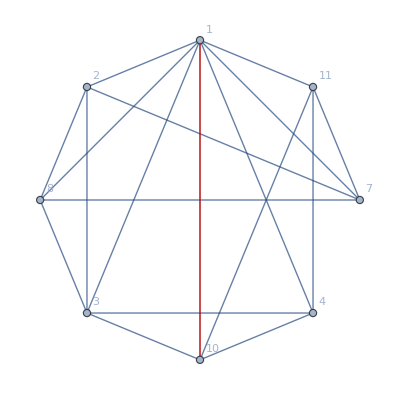
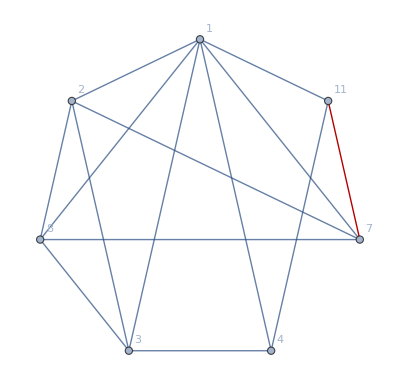
{{11<->12,-Graphics-},{13<->6,-Graphics-},{6<->9,-Graphics-},{6<->5,-Graphics-},{5<->16,-Graphics-},{5<->1,-Graphics-},{1<->10,-Graphics-},{11<->7,-Graphics-},{7<->4,-Graphics-}}

{11<->12,13<->6,6<->9,6<->5,5<->16,5<->1,1<->10,11<->7,7<->4}

```mathematica
work="";counted=0;currentEdges={};vertexCount=0;solution={};solution2={};
Monitor[FindContraction[g2435],{counted,currentEdges,vertexCount,work}];Print[solution]; Print[solution2]
```

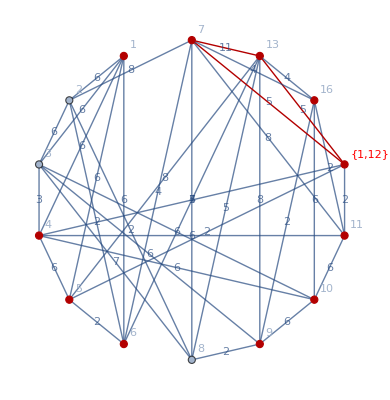

```mathematica
Graph[g2435, EdgeLabels->Table[e->(ChromaticPolynomial[EdgeContract[g2435,e],4]/24),{e,EdgeList[g2435]}],GraphHighlight->Flatten[Map[{#[[1]],#[[2]]}&,{11<->12,13<->6,6<->9,6<->5,5<->16,5<->1,1<->10,11<->7,7<->4}]]]
```